```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Read Results

```mathematica
InterpolateData[data_]:=Module[{temp},
temp = data;
(*Do[temp⟦ii⟧={{temp⟦ii,1⟧,temp⟦ii,2⟧},temp⟦ii,3⟧},{ii,1,Length[data]}];*)
Do[temp⟦ii⟧={temp⟦ii,1⟧,temp⟦ii,2⟧},{ii,1,Length[data]}];
Interpolation[temp,InterpolationOrder->1]
]
```

```mathematica
Clear[jOmega]
```

```mathematica
(*uExact[x_,y_]:=Sin[π x]Sin[π y];*)
uExact[x_]:=Exp[-(x-1)^2*100];
(*AdjExact[x_,y_]:=Sin[π x]Sin[π y];*)
AdjExact[x_,y_]:=Exp[-(x-0.5)^2*100-(y-0.5)^2*100];

cycles = 20;
```

```mathematica
Clear[resultPrimalInt,temp,errorVariation]
```

```mathematica
Do[resultPrimal[ii] =Import[StringJoin["../2D_advection_gaussian/result_cycle",ToString[ii],".txt"],"Table"];

,{ii,0,cycles-1}];

Do[resultAdj[ii] =Import[StringJoin["../2D_advection_gaussian/resultAdj_cycle",ToString[ii],".txt"],"Table"];errorPred[ii] =Import[StringJoin["../2D_advection_gaussian/error_predicted_cycle",ToString[ii],".txt"],"Table"];
errorObs[ii] =Import[StringJoin["../2D_advection_gaussian/error_observed_cycle",ToString[ii],".txt"],"Table"];
(*errorVariation[ii]=Transpose[{resultPrimal[ii]⟦All,1⟧,1/(2^(ii+1)10)jOmega[resultPrimal[ii]⟦All,1⟧]*(uExact[resultPrimal[ii]⟦All,1⟧]-resultPrimal[ii]⟦All,2⟧)}];*)
,{ii,0,cycles-2}];
```

## Compute Error

```mathematica
plotcycle=5;
ListPlot[{errorPred[plotcycle]⟦All,{1,3}⟧,errorObs[plotcycle]⟦All,{1,3}⟧},PlotMarkers->{"*","o","<"},PlotRange->Full,PlotMarkers->True,PlotLegends->{"pred","obs"},ImageSize->600]
```

-Graphics-

```mathematica
plotcycle=7;
ListPlot[{errorObs[plotcycle]⟦All,{1,3}⟧,errorObs[plotcycle+1]⟦All,{1,3}⟧},PlotMarkers->{"*","o","<"},PlotRange->Full,PlotMarkers->True,PlotLegends->{"obslow","obs"},ImageSize->600]
```

-Graphics-

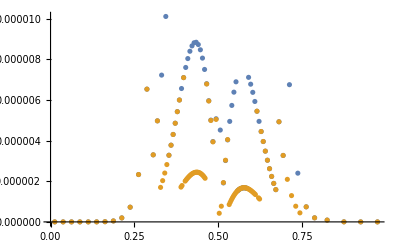

```mathematica
ListPlot[{Transpose[{errorObs[plotcycle]⟦All,1⟧,Abs[errorObs[plotcycle]⟦All,3⟧]}],Transpose[{errorObs[plotcycle+1]⟦All,1⟧,Abs[errorObs[plotcycle+1]⟦All,3⟧]}]}]
```

```mathematica
Total[errorObs[8]⟦All,3⟧]
```

-0.0000155169

```mathematica
convgAdp = Import["../2D_advection_gaussian/convergence_table_adaptive.txt","Table"];
convgUni = Import["../2D_advection_gaussian/convergence_table_uniform.txt","Table"];
```

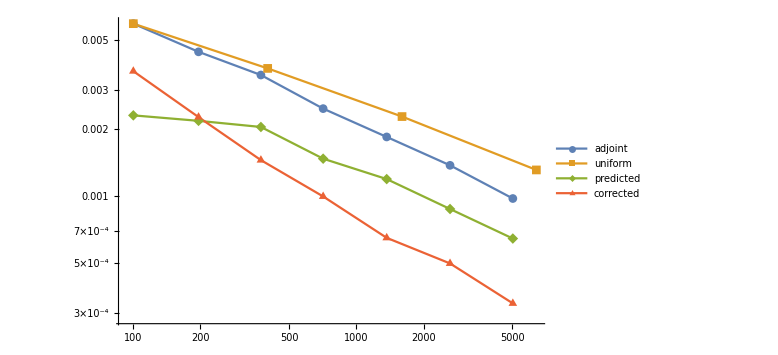

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,11}⟧},Joined->True,PlotLegends->{"adjoint","uniform","predicted","corrected"},PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Total[errorPred[2]⟦All,2⟧]
```

-0.608254

```mathematica
Total[errorPred[3]⟦All,2⟧]
```

-0.603729